## The article "Improved spatial speckle contrast model for tissue blood flow imaging: Effects of spatial correlation among neighboring camera pixels" in the Journal of Biomedical Optics (JBO) should be cited in any work related to the software .

```mathematica
MuInvFactor[m_,η_]:=(Exp[-π m (η-1)^2]-2Exp[-π m η^2]+Exp[-π m (η+1)^2]+π √m((η-1)Erf[√(π m)(η-1)]-2η Erf[√(π m)η]+(η+1)Erf[√(π m)(η+1)]))
MuInv[m_,η_,ξ_]:=1/(4 π^2 m^2)MuInvFactor[m,η]*MuInvFactor[m,ξ]
```

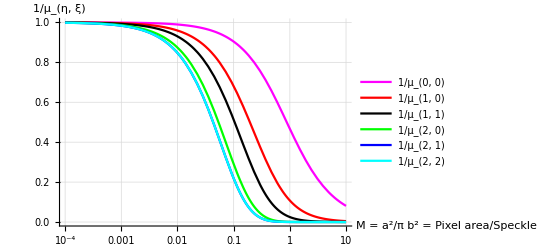

```mathematica
(*
%Calculating the correlation factors mu,for the first 6 correlation
%factors
*)
LogLinearPlot[{MuInv[m,0,0],MuInv[m,1,0],MuInv[m,1,1],MuInv[m,2,0],MuInv[m,2,1],MuInv[m,2,1]},{m,1*10^-4,10},PlotLegends->LineLegend[{"1/μ_(0, 0)","1/μ_(1, 0)","1/μ_(1, 1)","1/μ_(2, 0)","1/μ_(2, 1)","1/μ_(2, 2)"},LegendFunction->Frame],PlotStyle->{Magenta,Red,Black,Green,Blue,Cyan},GridLines->Automatic,AxesLabel->{"M = a^2/π b^2 = Pixel area/Speckle area","1/μ_(η, ξ)"}]
```

```mathematica
(*
%contraste espacial
% 2p+1≤sqrt(N)
% M=area pixel/area speckle
*)
Ks[m_,n_,p_]:=Module[{lateral,diagonal,knight,eta,xi,correccion,central, RETURN},
lateral=diagonal=knight=0;
central=MuInv[m,0,0];
If[n>1,
For[eta=1,eta≤p,eta++,
lateral=lateral+(√n-eta)√n MuInv[m,eta,0];
diagonal=diagonal+(√n-eta)^2 MuInv[m,eta,eta];
];(*end for p*)
lateral=4*lateral;
diagonal=4*diagonal;

For[xi=1,xi≤(p-1),xi++,
For[eta=xi+1,eta≤p,eta++,
knight=knight+(√n-eta)(√n-xi)MuInv[m,eta,xi];
](*fin del for eta*)
];(*fin del for xi*)
knight=8knight;
correccion=lateral+diagonal+knight;
correccion=correccion/(n(n-1));
,(*else*)
correccion=0;
];(*fin if*)
RETURN=central-correccion;
RETURN=√RETURN
]
```

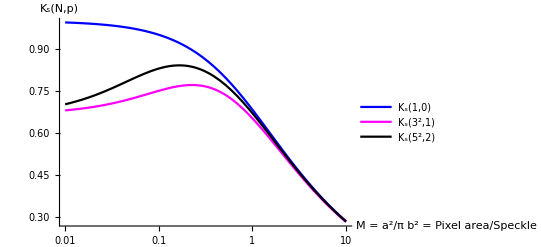

```mathematica
(*
%contrast for 1x1,3x3,5x5,7x7 sliding window respectively
*)
LogLinearPlot[{Ks[m,1^2,0],Ks[m,3^2,1],Ks[m,5^2,2]},{m,0.01,10},PlotLegends->LineLegend[{"K_s(1,0)","K_s(3^2,1)","K_s(5^2,2)"},LegendFunction->Frame],PlotStyle->{Blue,Magenta,Black},AxesLabel->{"M = a^2/π b^2 = Pixel area/Speckle area","K_s(N,p)"}]
```